# Swanepoel Fast Profile Calculator

This is a fast way to compare a given profile with the parameters you have already found. The information you must have is the following one:

The substrate refractive index ss

The refractive index function of the form n(λ)=a/λ^2+b

The film thickness d

The film absorption coefficient lnα(λ)=c/λ^2+ee

```mathematica
ss=1.534;
a=103527;
b=2.6765;
n[λ_]=a/λ^2+b;
d=1109.7444;
c=4*10^6;
ee=-14.067;
α[λ_]=E^(c/λ^2+ee);
```

The approximated coefficients are about to be calculated in order to get the whole information to construct the transmitances:

```mathematica
A[λ_]=16*n[λ]^2*ss;
B[λ_]=(n[λ]+1)^3*(n[λ]+ss^2);
Cc[λ_]=2*(n[λ]^2-1)*(n[λ]^2-ss^2);
Dd[λ_]=(n[λ]-1)^3*(n[λ]-ss^2);
ϕ[λ_]=(4*π*n[λ]*d)/λ;
x[λ_]=E^(-(α[λ]*d));
```

Now that functions are correctly defined and completely depending on the weavelenght, let’s proceed to draw the profiles according the given values and the model used:

```mathematica
T[λ_]=(A[λ]*x[λ])/(B[λ]-(Cc[λ]*x[λ]*Cos[ϕ[λ]])+(Dd[λ]*x[λ]^2));
TM[λ_]=(A[λ]*x[λ])/(B[λ]-(Cc[λ]*x[λ])+(Dd[λ]*x[λ]^2));
Tm[λ_]=(A[λ]*x[λ])/(B[λ]+(Cc[λ]*x[λ])+(Dd[λ]*x[λ]^2));
```

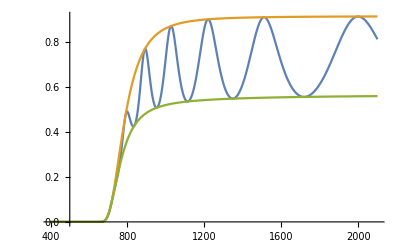

```mathematica
Plot[{T[λ],TM[λ],Tm[λ]},{λ,400,2100}]
```